```mathematica
(*f=Subscript[a, 5]*t^5+Subscript[a, 4]*t^4+Subscript[a, 3]*t^3+Subscript[a, 2]*t^2+Subscript[a, 1]*t+Subscript[a, 0];*)
f=Subscript[a, 5]*t^5+Subscript[a, 4]*t^4+Subscript[a, 3]*t^3+Subscript[a, 2]*t^2+Subscript[a, 1]*t+Subscript[a, 0];
```

```mathematica
D[f,t]
```

a_1+2 t a_2+3 t^2 a_3+4 t^3 a_4+5 t^4 a_5

```mathematica
eqn1=x0-f==0/.t->t0
```

x0-a_0-t0 a_1-t0^2 a_2-t0^3 a_3-t0^4 a_4-t0^5 a_5==0

```mathematica
eqn2=xf-f==0/.t->tf
```

xf-a_0-tf a_1-tf^2 a_2-tf^3 a_3-tf^4 a_4-tf^5 a_5==0

```mathematica
eqn3=hmax-f==0/.t->(t0+tf)/2
```

hmax-a_0-1/2 (t0+tf) a_1-1/4 (t0+tf)^2 a_2-1/8 (t0+tf)^3 a_3-1/16 (t0+tf)^4 a_4-1/32 (t0+tf)^5 a_5==0

```mathematica
eqn4=D[f,t]==0/.t->(t0+tf)/2
```

a_1+(t0+tf) a_2+3/4 (t0+tf)^2 a_3+1/2 (t0+tf)^3 a_4+5/16 (t0+tf)^4 a_5==0

```mathematica
eqn5=D[f,t]==vf/.t->tf
```

a_1+2 tf a_2+3 tf^2 a_3+4 tf^3 a_4+5 tf^4 a_5==vf

```mathematica
eqn6=D[f,t]==0/.t->t0
```

a_1+2 t0 a_2+3 t0^2 a_3+4 t0^3 a_4+5 t0^4 a_5==0

```mathematica
eqnSubs = Solve[{eqn1,eqn2,eqn3,eqn4,eqn5,eqn6},{Subscript[a, 0],Subscript[a, 1],Subscript[a, 2],Subscript[a, 3],Subscript[a, 4],Subscript[a, 5]}]//FullSimplify
```

{{a_0→(16 hmax t0^2 (t0-tf) tf^2+(t0+tf)^2 (tf (t0^2 (-t0+tf) vf+(7 t0-tf) tf x0)+t0^2 (t0-7 tf) xf))/(t0-tf)^5,a_1→(t0 (t0+tf) (32 hmax tf (-t0+tf)+t0^3 vf+6 t0^2 tf vf-2 tf^2 (tf vf+23 x0-7 xf)+t0 tf (-5 tf vf-14 x0+46 xf)))/(t0-tf)^5,a_2→(16 hmax (t0-tf) (t0^2+4 t0 tf+tf^2)-6 t0^4 vf+t0 tf^2 (11 tf vf+129 x0-81 xf)+3 t0^2 tf (3 tf vf+27 x0-43 xf)+t0^3 (-15 tf vf+7 x0-23 xf)+tf^3 (tf vf+23 x0-7 xf))/(t0-tf)^5,a_3→(32 hmax (-t0^2+tf^2)+13 t0^3 vf+tf^2 (-5 tf vf-66 x0+34 xf)+t0^2 (9 tf vf-34 x0+66 xf)+t0 tf (-17 tf vf-140 x0+140 xf))/(t0-tf)^5,a_4→(4 (4 hmax (t0-tf)-3 t0^2 vf+t0 (tf vf+13 x0-17 xf)+tf (2 tf vf+17 x0-13 xf)))/(t0-tf)^5,a_5→(4 (t0 vf-tf vf-6 x0+6 xf))/(t0-tf)^5}}

```mathematica
x0=0;
xf=-0.2;
t0=0;
tf=2;
hmax=0.3;
vf=-0.3
```

-0.3

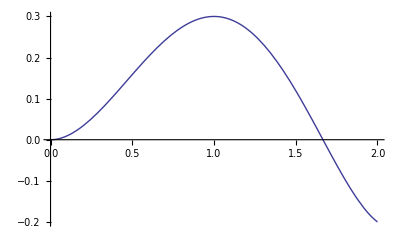

```mathematica
Plot[f/.eqnSubs,{t,t0,tf}]
```